### 2)

```mathematica
A={{1,-3,2,0},{0,-6.4,5.4,1}}
b={1,2,-1,3.4}
x=LinearSolve[A.Transpose[A],A.b]
```

{{1,-3,2,0},{0,-6.4,5.4,1}}

{1,2,-1,3.4}

{-0.562709,0.0292642}

```mathematica
c=x[[1]]*A[[1]]+x[[2]]*A[[2]]
```

{-0.562709,1.50084,-0.967391,0.0292642}

```mathematica
(b-c).A[[1]]
(b-c).A[[2]]
```

2.22045×10^-15

3.10862×10^-15

### 3)

```mathematica
Clear["Global`*"]
```

```mathematica
b={2,2,3.7,0.5,-1}
A=Transpose[{{1,2.17,1,3,0.56},{1,1,1,1,1}}]
x=LinearSolve[Transpose[A].A,Transpose[A].b]
Transpose[A].A
Transpose[A].b
```

{2,2,3.7,0.5,-1}

{{1,1},{2.17,1},{1,1},{3,1},{0.56,1}}

{-0.0371324,1.49741}

{{16.0225,7.73},{7.73,5.}}

{10.98,7.2}

```mathematica
MatrixForm[x]
```

(-0.0371324
1.49741)

```mathematica
b={2,2,3.7,0.5,-1}
A=Transpose[{{1,4.7089,1,9,0.3136},{1,2.17,1,3,0.56},{1,1,1,1,1}}]
x=LinearSolve[Transpose[A].A,Transpose[A].b]
```

{2,2,3.7,0.5,-1}

{{1,1,1},{4.7089,2.17,1},{1,1,1},{9,3,1},{0.3136,0.56,1}}

{-2.28234,8.15924,-3.86043}

```mathematica
b={2,2,3.7,0.5,-1}
A=Transpose[{{Sqrt[1],Sqrt[2.17],Sqrt[1],Sqrt[3],Sqrt[0.56]},{1,1,1,1,1}}]
x=LinearSolve[Transpose[A].A,Transpose[A].b]
```

{2,2,3.7,0.5,-1}

{{1,1},{1.47309,1},{1,1},{√3,1},{0.748331,1}}

### 5)

```mathematica
Clear["Global`*"]
```

```mathematica
Uno[x_]:=1
Id[x_]:=x
f[x_]:=x+2x^2
e[x_]:=Exp[x/Pi]
B={Id,Cos,Uno,e}
productoescalar[f_,g_]:=Integrate[f[x]*g[x],{x,0,Pi}]
A=Table[productoescalar[B[[i]],B[[j]]],{i,1,4},{j,1,4}]
b=Table[productoescalar[B[[i]],f],{i,1,4}]
c=LinearSolve[A,b]//N
```

{Id,Cos,Uno,e}

{{π^3/3,-2,π^2/2,π^2},{-2,π/2,0,-((1+ⅇ) π)/(1+π^2)},{π^2/2,0,π,(-1+ⅇ) π},{π^2,-((1+ⅇ) π)/(1+π^2),(-1+ⅇ) π,1/2 (-1+ⅇ^2) π}}

{π^3/3+π^4/2,-2-4 π,π^2/2+(2 π^3)/3,π^2+2 (-2+ⅇ) π^3}

{-6.49862,-1.45535,-22.0572,23.521}

```mathematica
p[x_]:=-6.49862B[[1]][x]-1.45535B[[2]][x]-22.0572B[[3]][x]+23.521B[[4]][x]
```

```mathematica
p[x]
```

-22.0572+23.521 ⅇ^(x/π)-6.49862 x-1.45535 Cos[x]

```mathematica
diff[x_]:=f[x]-p[x]
```

```mathematica
Table[productoescalar[diff,B[[i]]],{i,4}]
```

{0.00022831,-0.000046273,0.00010723,0.000216929}

### 6)

```mathematica
p={0,0.3,0.9,1.1,1.5}
n=Length[p]-1
```

{0,0.3,0.9,1.1,1.5}

4

```mathematica
B[i_,x_]:=If[i<n,Which[p[[i]]≤x≤p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),p[[i+1]]≤x≤p[[i+2]],(p[[i+2]]-x)/(p[[i+2]]-p[[i+1]]),True,0],Which[p[[i]]≤x≤p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),True,0]]
```

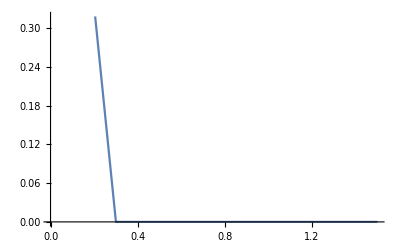
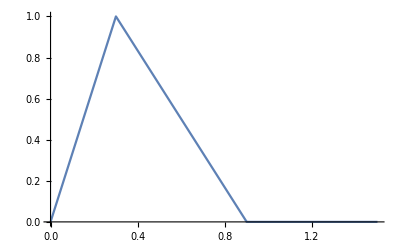
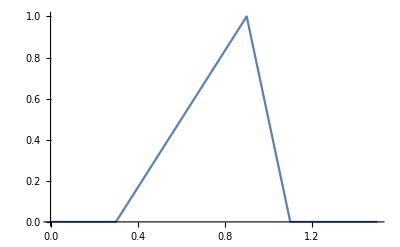
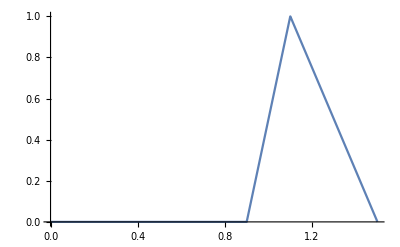
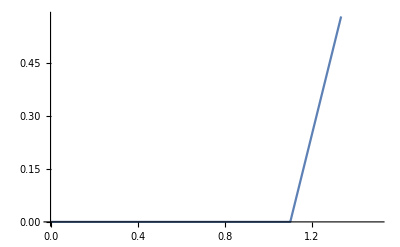

```mathematica
Table[Plot[B[i,x],{x,p[[1]],p[[n+1]]}],{i,0,n}]
```

```mathematica
f[x_]:=x^2
```

```mathematica
s[x_]:=Sum[B[i,x]*f[p[[i+1]]],{i,0,n}]
```

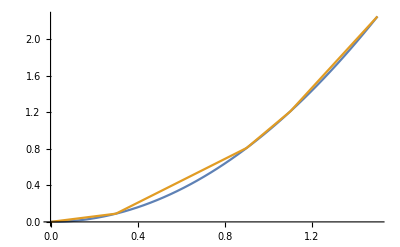

```mathematica
Plot[{f[x],s[x]},{x,p[[1]],p[[n+1]]}]
```

### 10)

```mathematica
Clear["Global`*"]
```

```mathematica
nodos1=Table[Cos[(2i+1)Pi/14],{i,0,6}]
```

{Cos[π/14],Cos[(3 π)/14],Sin[π/7],0,-Sin[π/7],-Cos[(3 π)/14],-Cos[π/14]}

```mathematica
g[x_]:=0.7x+2.3
```

```mathematica
nodos=Table[g[nodos1[[8-i]]],{i,1,7}]
```

{1.61755,1.75272,1.99628,2.3,2.60372,2.84728,2.98245}

```mathematica
f[x_]:=Sqrt[Abs[x-2]]
```

```mathematica
BL=Table[0,{j,7}];      (* Lagrange *)
For[i=1,i≤7,i++,BL[[i]]=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,1,7}]]
```

```mathematica
q[x_]:=Collect[Sum[BL[[i]]*f[nodos[[i]]],{i,1,7}],x]
```

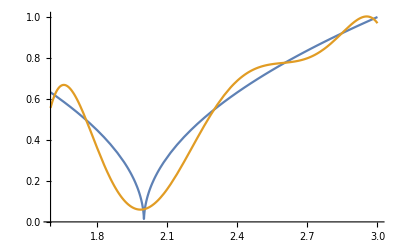

```mathematica
Plot[{f[x],q[x]},{x,1.6,3}]
```

```mathematica
BN=Table[0,{j,7}];   (* Newton *)
For[i=1,i≤7,i++,BN[[i]]=Product[(x-nodos[[j]]),{j,1,i-1}]]
```

```mathematica
dd=Table[0,{i,7},{j,7}];
For[i=1,i≤7,i++,dd[[i,1]]=f[nodos[[i]]]]
For[i=2,i≤7,i++,For[j=2,j≤i,j++,dd[[i,j]]=(dd[[i,j-1]]-dd[[i-1,j-1]])/(nodos[[i]]-nodos[[i-j+1]])]]
```

```mathematica
q[x_]:=Collect[Sum[dd[[i,i]]*BN[[i]],{i,7}],x]
```

```mathematica
Plot[{f[x],q[x]},{x,1.6,3}]
```

```mathematica
(* Error, con lagrange *)
```

```mathematica
lambaN[x_]:=Sum[Abs[BL[[i]]],{i,1,7}]
```

```mathematica
FindMaximum[{lambaN[x],1.6≤x≤3},{x,3}]
```

{2.20221,{x→3.}}

```mathematica
Plot[lambaN[x],{x,1.6,3}]
```

```mathematica
FindMaximum[{lambaN[x],1.6≤x≤3},{x,3}]
```

{2.20221,{x→3.}}

```mathematica
cteLeb=2.20221    (* Buen condicionamiento *)
```

2.20221

### 11)

```mathematica
nodos=Table[-1+i/4,{i,0,8}]
chev=Table[Cos[(1+2i)Pi/18],{i,0,8}]//N
```

{-1,-3/4,-1/2,-1/4,0,1/4,1/2,3/4,1}

{0.984808,0.866025,0.642788,0.34202,0.,-0.34202,-0.642788,-0.866025,-0.984808}

```mathematica
baseLagrange[nodos_]:=Block[{n=Length[nodos],l=Table[0,{k,Length[nodos]}],i,x},For[i=1,i≤n,i++,l[[i]]=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,n}]];l]
```

```mathematica
B1=baseLagrange[nodos];
B2=baseLagrange[chev];
```

```mathematica
f[x_]:=2Abs[x]+1
```

```mathematica
p1[x_]:=Collect[Sum[f[nodos[[i]]]*B1[[i]],{i,1,Length[B1]}],x]
```

```mathematica
p2[x_]:=Collect[Sum[f[chev[[i]]]*B2[[i]],{i,1,Length[B2]}],x]
```

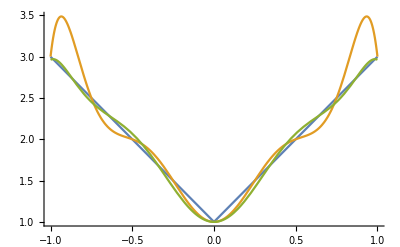

```mathematica
Plot[{f[x],p1[x],p2[x]},{x,-1,1}]
```

### 12)

```mathematica
Clear["Global`*"]
```

```mathematica
nodos={-2,-1,0,1};
y={1,0,0,0.4};
d={1.2,-1,0,1};
n=Length[nodos];
```

```mathematica
BL[i_,x_]:=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,1,n}]
```

```mathematica
dL[i_,x_]:=D[BL[i,t],t]/.t->x
```

```mathematica
H2[i_,x_]:=(1-2(x-nodos[[i]])*dL[i,nodos[[i]]])*BL[i,x]^2
H1[i_,x_]:=(x-nodos[[i]])BL[i,x]^2
```

```mathematica
Clear[p]
```

```mathematica
p[x_]:=Sum[y[[i]]*H2[i,x]+d[[i]]*H1[i,x],{i,1,n}]
```

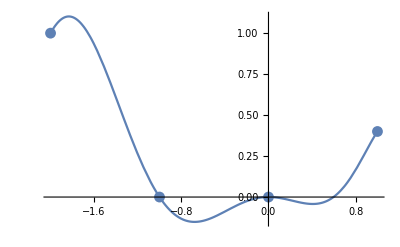

```mathematica
Show[Plot[p[x],{x,nodos[[1]],nodos[[n]]},PlotRange->All],ListPlot[Table[{nodos[[i]],y[[i]]},{i,1,n}],PlotRange->All]]
```

### 13)

```mathematica
f[x_]:=1/(1+25x^2)
```

```mathematica
p=Table[-1+2i/5,{i,0,5}]
n=Length[p]-1
```

{-1,-3/5,-1/5,1/5,3/5,1}

5

```mathematica
(* Lineales *)
```

```mathematica
B[i_,x_]:=If[i<n,Which[p[[i]]≤x≤p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),p[[i+1]]≤x<p[[i+2]],(p[[i+2]]-x)/(p[[i+2]]-p[[i+1]]),True,0],Which[p[[i]]≤x≤p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),True,0],0]
```

```mathematica
q[x_]:=Collect[Sum[B[i,x]*f[p[[i+1]]],{i,0,n}],x]
```

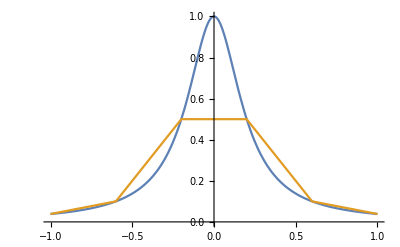

```mathematica
Plot[{f[x],q[x]},{x,p[[1]],p[[n+1]]}]
```

```mathematica
(* Cúbicas *)
```

```mathematica
h=(p[[n+1]]-p[[1]])/n;
A=2IdentityMatrix[n+1];
For[i=1,i<n,i++,A[[i+1,i]]=1/2;A[[i+1,i+2]]=1/2]
Y=Table[0,{j,n+1}];
For[i=2,i≤n,i++,Y[[i]]=f[p[[i+1]]]-2f[p[[i]]]+f[p[[i-1]]]]
c=LinearSolve[A,3Y/h^2]
```

{0,1020/247,-945/247,-945/247,1020/247,0}

```mathematica
s[i_,x_]:=Which[p[[i]]≤x≤p[[i+1]],c[[i]](p[[i+1]]-x)^3/(6h)+c[[i+1]](x-p[[i]])^3/(6h)+((f[p[[i+1]]]-f[p[[i]]])/h-h/6(c[[i+1]]-c[[i]]))(x-p[[i]])+f[p[[i]]]-c[[i]] h^2/6,True,0]
```

```mathematica
S[x_]:=Sum[s[i,x],{i,1,n}]
```

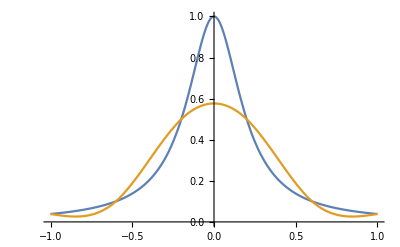

```mathematica
Plot[{f[x],S[x]},{x,p[[1]],p[[n+1]]}]
```

```mathematica
(* Principio de mínima energía *)
```

```mathematica
BL[i_,x_]:=Product[If[j≠i,(x-p[[j]])/(p[[i]]-p[[j]]),1],{j,1,n+1}]
```

```mathematica
BL[6,x]
```

625/768 (-3/5+x) (-1/5+x) (1/5+x) (3/5+x) (1+x)

```mathematica
g[x_]:=Collect[Sum[BL[i,x]*f[p[[i]]],{i,1,n+1}],x]
```

```mathematica
Integrate[S''[x]^2,{x,p[[1]],p[[n+1]]}]//N
```

14.6403

```mathematica
Integrate[g''[x]^2,{x,p[[1]],p[[n+1]]}]//N
```

40.6065